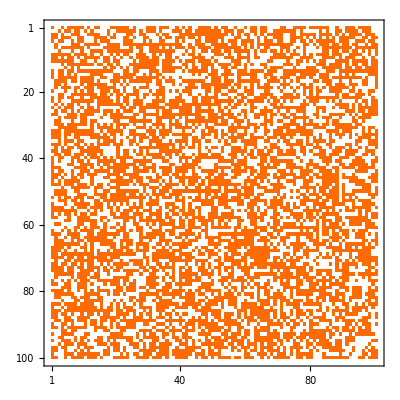

```mathematica
A=Module[{p=.6},Table[If[RandomReal[]<p,1,0],{i,100},{j,100}]];
MatrixPlot[A]
```

```mathematica
ClearAll[counts]
counts[m_]:=#/.ComponentMeasurements[#,"Count"]&@MorphologicalComponents[m,CornerNeighbors->False]
```

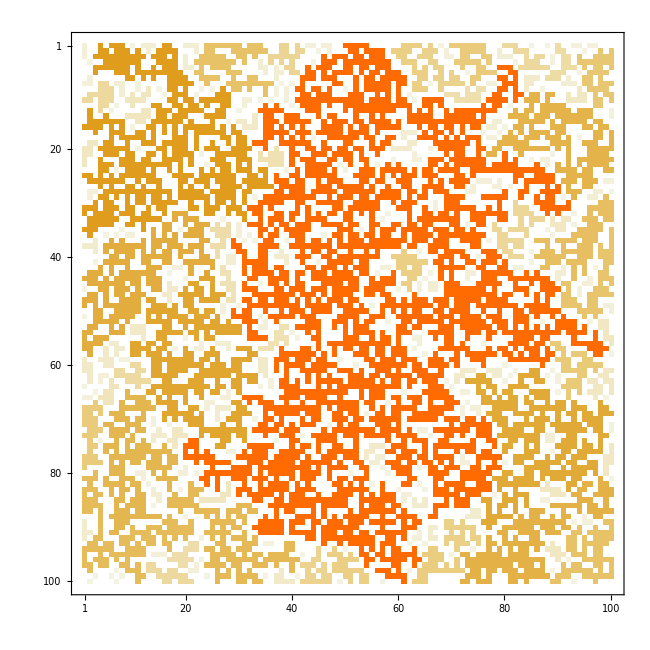

```mathematica
MatrixPlot[counts[A]]
```

```mathematica
Union[Join@@counts[m]]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,14,15,17,18,19,20,21,22,26,32,33,39,43,44,66,75,177,197,228,341,433,741,2665}

```mathematica
m=A;
```

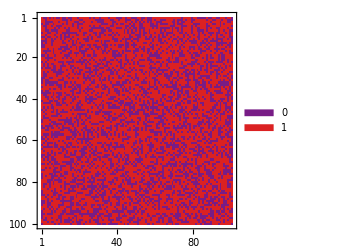
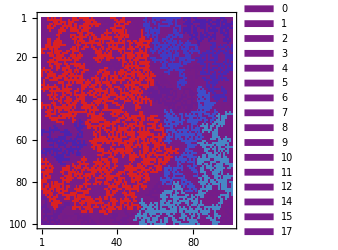

```mathematica
cnts=Union[Join@@counts[m]];

Row[{MatrixPlot[m,ImageSize->250,ColorFunction->"Rainbow",ColorFunctionScaling->False,PlotLegends->SwatchLegend["Rainbow",{0,1}]],MatrixPlot[counts@m,ImageSize->250,ColorFunction->ColorData[{"Rainbow",{0,Max[cnts]}}],ColorFunctionScaling->False,PlotLegends->SwatchLegend[ColorData["Rainbow"]/@Rescale[cnts],cnts]]},Spacer[10]]
```

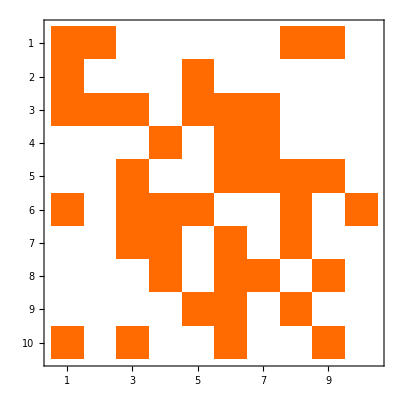

```mathematica
A=Module[{p=.6},Table[If[RandomReal[]<p,1,0],{i,10},{j,10}]];
MatrixPlot[A]
```

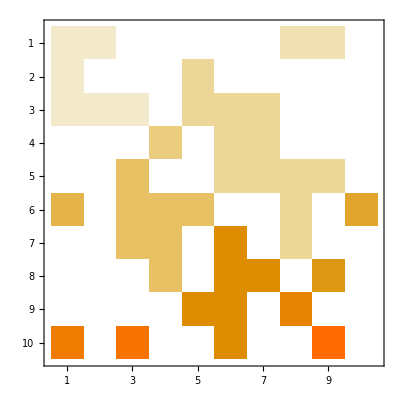

```mathematica
MorphologicalComponents[A,CornerNeighbors->False]//MatrixPlot
```

```mathematica
MorphologicalComponents[A,CornerNeighbors->False]//MatrixForm
```

(1 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0
1 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 3 | 3 | 3 | 0 | 0 | 0
0 | 0 | 0 | 4 | 0 | 3 | 3 | 0 | 0 | 0
0 | 0 | 5 | 0 | 0 | 3 | 3 | 3 | 3 | 0
6 | 0 | 5 | 5 | 5 | 0 | 0 | 3 | 0 | 7
0 | 0 | 5 | 5 | 0 | 9 | 0 | 3 | 0 | 0
0 | 0 | 0 | 5 | 0 | 9 | 9 | 0 | 8 | 0
0 | 0 | 0 | 0 | 9 | 9 | 0 | 10 | 0 | 0
11 | 0 | 12 | 0 | 0 | 9 | 0 | 0 | 13 | 0)

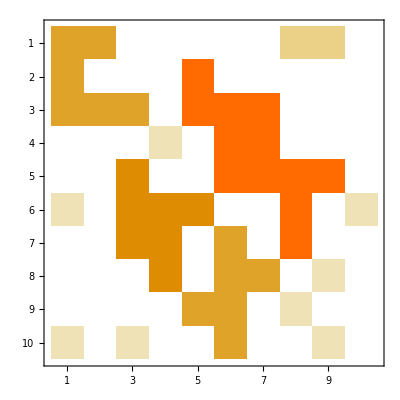

```mathematica
#/.ComponentMeasurements[#,"Count"]&@MorphologicalComponents[A,CornerNeighbors->False]//MatrixPlot
```

```mathematica
#/.ComponentMeasurements[#,"Count"]&@MorphologicalComponents[A,CornerNeighbors->False]//MatrixForm
```

(6 | 6 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0
6 | 0 | 0 | 0 | 12 | 0 | 0 | 0 | 0 | 0
6 | 6 | 6 | 0 | 12 | 12 | 12 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 12 | 12 | 0 | 0 | 0
0 | 0 | 7 | 0 | 0 | 12 | 12 | 12 | 12 | 0
1 | 0 | 7 | 7 | 7 | 0 | 0 | 12 | 0 | 1
0 | 0 | 7 | 7 | 0 | 6 | 0 | 12 | 0 | 0
0 | 0 | 0 | 7 | 0 | 6 | 6 | 0 | 1 | 0
0 | 0 | 0 | 0 | 6 | 6 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0 | 6 | 0 | 0 | 1 | 0)

```mathematica
#/.ComponentMeasurements[#,"Count"]&@MorphologicalComponents[A,CornerNeighbors->False]
```

{{6,6,0,0,0,0,0,2,2,0},{6,0,0,0,12,0,0,0,0,0},{6,6,6,0,12,12,12,0,0,0},{0,0,0,1,0,12,12,0,0,0},{0,0,7,0,0,12,12,12,12,0},{1,0,7,7,7,0,0,12,0,1},{0,0,7,7,0,6,0,12,0,0},{0,0,0,7,0,6,6,0,1,0},{0,0,0,0,6,6,0,1,0,0},{1,0,1,0,0,6,0,0,1,0}}

```mathematica
c=KeyDrop[Counts@(Join@@#/.ComponentMeasurements[#,"Count"]&@MorphologicalComponents[A,CornerNeighbors->False]),0]
```

<|6→12,2→2,12→12,1→8,7→7|>

```mathematica
KeyValueMap[#1->#2/#1&,c]
```

{6→2,2→1,12→1,1→8,7→1}